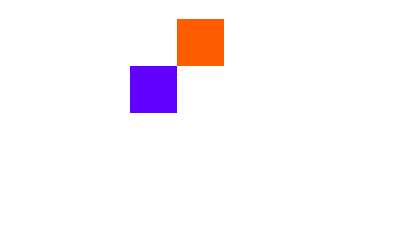
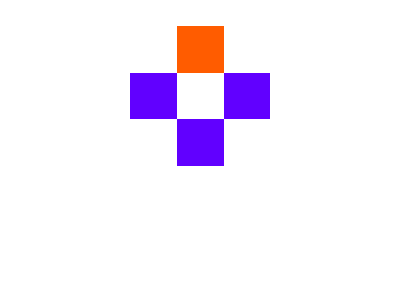
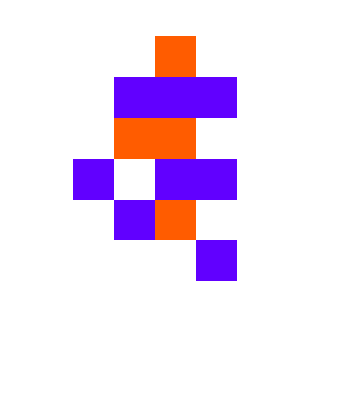
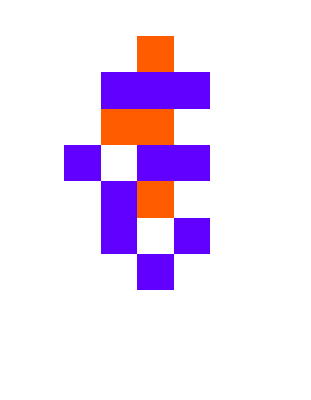
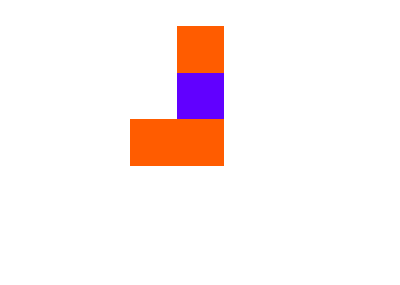
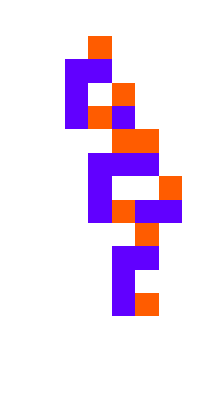
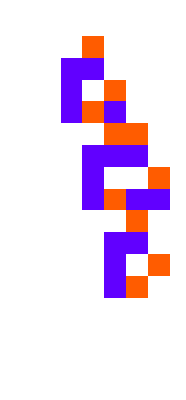
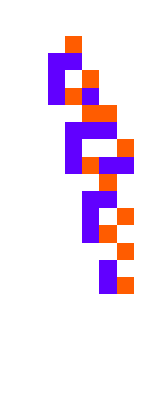
{{-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

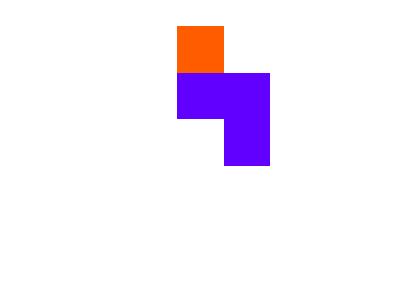
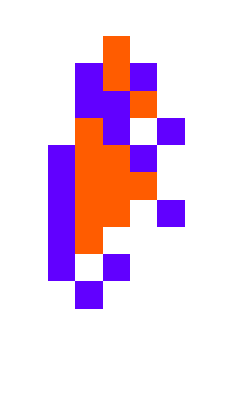
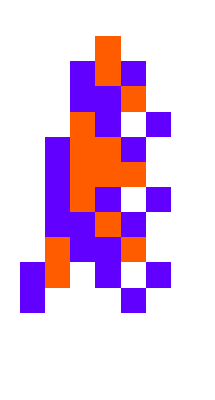
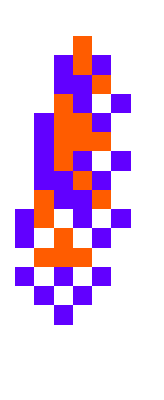
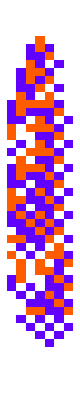
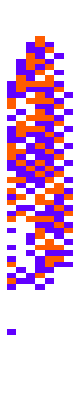
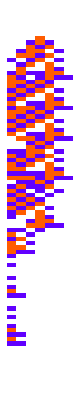
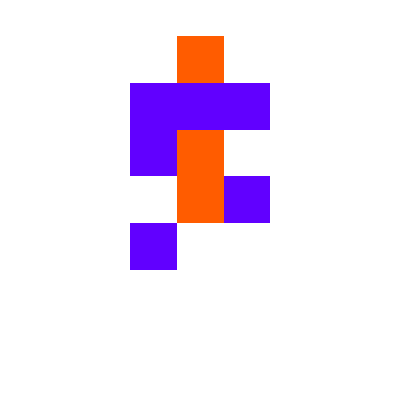
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[
SeedRandom[222344 + i];ArrayPlot[CellularAutomaton[#rule, {{1}, 0}, {#fitness+1, {-3, 3}}], ImageSize->12Sqrt[#fitness]]&/@ GatherBy[AdaptiveSearch[CellularAutomaton[{0, 3, 1}], 1000], Last][[All, 1]], {i, 10}]
```

```mathematica
AdaptiveSearch[CellularAutomaton[{0, 3, 1}], 1]
```

{{774840978,3,1},1}

{<|rule→{0,3,1},fitness→1|>,<|rule→{774840978,3,1},fitness→1|>}

```mathematica
Table[SeedRandom[222333 + i];ArrayPlot[CellularAutomaton[#rule, {{1}, 0}, {#fitness+1, {-3, 3}}], ImageSize->12Sqrt[#fitness]]&/@ GatherBy[AdaptiveSearch[CellularAutomaton[{0, 3, 1}], 1000], Last][[All, 1]], {i, 10}]
```

```mathematica
SeedRandom[222344 + 8];ArrayPlot[CellularAutomaton[#rule, {{1}, 0}, {#fitness+1, {-3, 8}}], ImageSize->12Sqrt[#fitness]]&/@ GatherBy[AdaptiveSearch[CellularAutomaton[{0, 3, 1}], 1000], Last][[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[222344 + 3];ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, RandomInteger[2, 100], {50,All}], ImageSize->Automatic]&/@ GatherBy[
AdaptiveSearch[CellularAutomaton[{0, 3, 1}], 30, "FitnessFunction"-> (StringLength[Compress[CellularAutomaton[#, RandomInteger[2, 100], 100]]]&)],
 Last][[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[222344 + 8];ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#rule, RandomInteger[2, 100], {50,All}], ImageSize->Automatic]&/@ GatherBy[AdaptiveSearch[CellularAutomaton[{ResourceFunction["RandomCA"][{3, 1}]["RuleNumber"], 3, 1}], 30, "FitnessFunction"-> (-StringLength[Compress[CellularAutomaton[#, RandomInteger[2, 100], 100]]]&)], Last][[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ClearAll[AdaptiveSearch];Options[AdaptiveSearch] = {"MutationFunction"->( {{"[◼]", "RandomRuleMutation"}}), "FitnessFunction"->( {{"[◼]", "TestLifetime"}}[#, 100]&),"SelectionFunction"->(#1>= #2&), "InitialFitness"->Automatic, "HaltCondition"->None};
AdaptiveSearch[sys_, steps_, OptionsPattern[AdaptiveSearch]]:=Module[{rule},
rule = First[sys];
NestList[
(Block[{newrule= OptionValue["MutationFunction"][#rule], newfitness},
newfitness = OptionValue["FitnessFunction"][newrule];
AssociationThread[{"rule", "fitness"}-> If[OptionValue["SelectionFunction"][newfitness, #fitness], {newrule, newfitness}, {#rule, #fitness}]]]
&),
<|"rule"-> rule, "fitness"-> If[OptionValue["InitialFitness"] === Automatic, OptionValue["FitnessFunction"][rule], OptionValue["InitialFitness"]]|>,
steps
]
]
```

```mathematica
ClearAll[AdaptiveSearch];
Options[AdaptiveSearch] = {"MutationFunction"->( {{"[◼]", "RandomRuleMutation"}}), "FitnessFunction"->( {{"[◼]", "TestLifetime"}}[#, 100]&),"SelectionFunction"->(#1>= #2&), "InitialFitness"->Automatic, "HaltCondition"->None};
AdaptiveSearch[x_, y_, OptionsPattern[AdaptiveSearch]]:= {x, y}
```

```mathematica
searches = ParallelTable[
SeedRandom[444110 + i];
AdaptiveSearch[CellularAutomaton[{0, 4, 1}], 1], {i, 1}]
```

TerminatedEvaluation[RecursionLimit]

TerminatedEvaluation[RecursionLimit]

```mathematica
ParallelTable[SeedRandom[444110 + i];{{"[◼]", "RandomRuleMutation"}}[{0, 4, 1}, 1,"Symmetric"->True],{i, 10}]
```

{{75557863725914323419136,4,1},{4294967300,4,1},{618970019642690137986433024,4,1},{216172782315110400,4,1},{309485009821345068993216512,4,1},{562949953945600,4,1},{37778931898141533798400,4,1},{885443715538058477568,4,1},{50331648,4,1},{75557863725914323419136,4,1}}